```mathematica
(*SetDirectory[FileNameJoin[{$HomeDirectory,"Box Sync","Gay Group","Project - Rb Spin Filter"}]]*)
Import[FileNameJoin[{$PACKAGES,"absorption.wl"}]]
```

```mathematica
$PACKAGES
```

C:\Users\kahrendsen2\Box Sync\Gay Group\Project - Rb Spin Filter\karl\mathematicaRb\packages

```mathematica
fn=FileNames["*.dat"]
```

{}

{Dashing[{}],Dashing[{Small,Small}],Dashing[{0,Small}],Dashing[{0,Small,Small,Small}]}

{40.,50.,60.,70.,80.,90.,100.,110.}

{40.°C, 4.2×10^10,50.°C, 1.1×10^11,60.°C, 2.5×10^11,70.°C, 5.6×10^11,80.°C, 1.2×10^12,90.°C, 2.4×10^12,100.°C, 4.8×10^12,110.°C, 9.1×10^12}

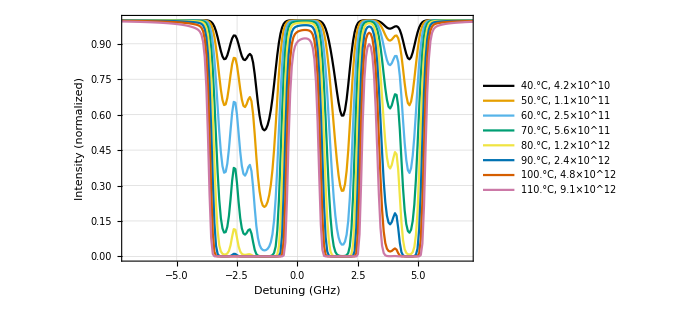

Dashing[{Small,Small}]

{110.°C, 9.1×10^12,120.°C, 1.7×10^13,130.°C, 2.9×10^13,140.°C, 5.1×10^13,150.°C, 8.5×10^13,160.°C, 1.4×10^14,170.°C, 2.2×10^14,180.°C, 3.4×10^14}

General::munfl: 1.609366268119691×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.028029031036906×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.552575678124823×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

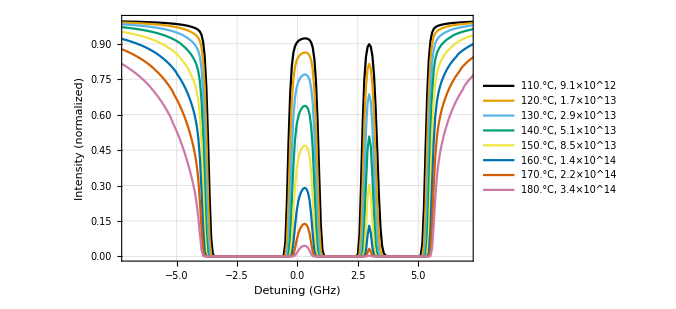

```mathematica
(* Plot the data for all curves *)
(* These are the temperatures for which we simulated the profiles. *)
temps=Range[313.15,453.15,10]-273.15;
(* All of the files in this folder, save the last one represent one scan at a given temperature.*)
absProfileFiles=fn[[;;-2]];
(* The last file represents the frequencies at which each line in the data file was simulated.*)
frequencyFile=fn[[-1]];
frequencies=Transpose[Import[frequencyFile,"csv"]][[1]];
(* This for loop reads all the information from the files and puts it into a Mathematica List. *)
allData={};
For[i=1,i≤Length[absProfileFiles],i++,
data=Transpose[Import[absProfileFiles[[i]],"csv"]][[1]];
AppendTo[allData,Transpose[{frequencies,data}]];
]
(* Since there are 15 absorption files, it's wise to split it up into two plots, low temperature and high temperature. The division represents where that split occurs.*)
division=8;
(* The code for the first plot. *)
dashings={Dashing[{}],Dashed, Dotted,DotDashed}
takeRange={1,division};
allData1=Take[allData,takeRange];
temps1=Take[temps,takeRange]
densityStrings=Thread[SetPrecision[RbNDensity[temps1+273.15],2]];
(*ll=legend labels *)
ll=Apply[StringJoin[ToString[#1],"°C, ",ToString[#2,TraditionalForm]]&,Transpose[{temps1,densityStrings}],{1}]
ListPlot[allData1,Joined->True,PlotRange->{{-7,7},Full},PlotLegends->ll,absLabels,PlotStyle->colorBlindPalette,ImageSize->500]
Dashed
(* The code for the second plot. *)
takeRange={division,-1};
allData=Take[allData,takeRange];
temps=Take[temps,takeRange];
tempsStrings=ToString[Thread[ToString[temps]]];
densityStrings=Thread[SetPrecision[RbNDensity[temps+273.15],2]];
ll=Apply[StringJoin[ToString[#1],"°C, ",ToString[#2,TraditionalForm]]&,Transpose[{temps,densityStrings}],{1}]
ListPlot[allData,Joined->True,PlotRange->{{-7,7},Full},PlotLegends->ll,absLabels,PlotStyle->colorBlindPalette,ImageSize->500]
```

D1AbsorptionData_t=363.15_Lc=0.03.dat

90°C, 2.4×10^12 atoms*cm^-3

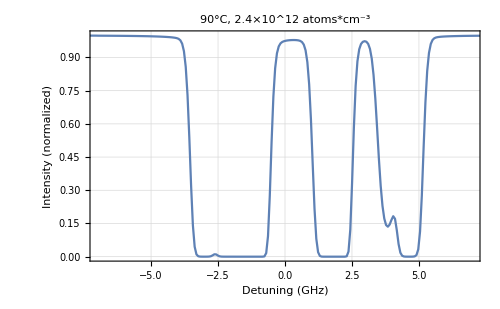

```mathematica
(* Plot a single curve *)
(* Plot the data for all curves *)
temperature=90; (* In degree C *)
kelvinTemp=273.15+temperature;
fileName="D1AbsorptionData_t="<>ToString[kelvinTemp]<>"_Lc=0.03.dat"
frequencies=Transpose[Import[fn[[-1]],"csv"]][[1]];

data=Transpose[Import[fileName,"csv"]][[1]];
allData=Transpose[{frequencies,data}];
densityString=Thread[SetPrecision[RbNDensity[temperature+273.15],2]];
(*ll=legend labels *)
ll=StringJoin[ToString[temperature],"°C, ",ToString[densityString,TraditionalForm]," atoms*cm^-3"]
ListPlot[allData,Joined->True,PlotRange->{{-7,7},Full},PlotLabel->ll,absLabels,ImageSize->500]
```

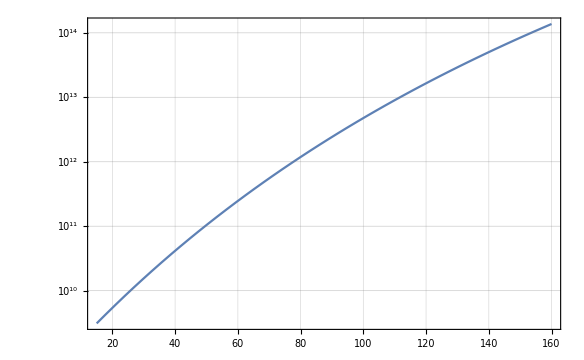

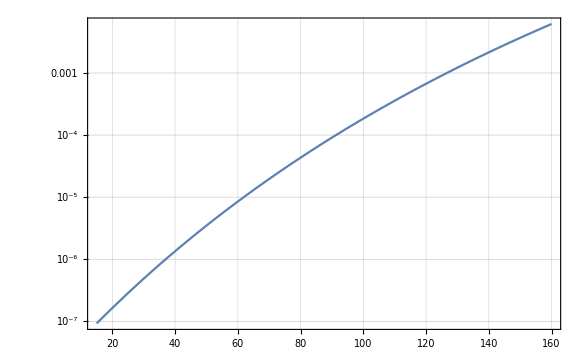

```mathematica
LogPlot[RbNDensity[x+273],{x,15,160}]
LogPlot[RbPressure[x+273],{x,15,160}]
```